### Sources

https://en.wikipedia.org/wiki/Airy_disk
https://www.cambridgeincolour.com/tutorials/diffraction-photography.htm
https://en.wikipedia.org/wiki/F-number

## Airy Disks

```mathematica
focalLength = 100 Quantity[, "Millimeters"]; 
λ= 700 Quantity[, "Nanometers"]
pupilDiameter = focalLength/fNumber;
numericalAperture := 1/(√(4 fNumber^2+1));
```

700 nm

The radius of the first dark band:

```mathematica
q1 := 1.22 * λ/(2numericalAperture);
```

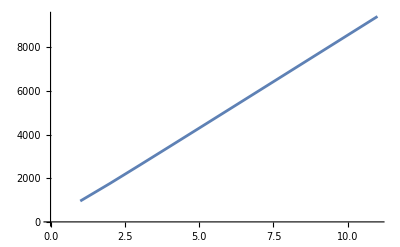

```mathematica
ListLinePlot[Table[q1, {fNumber, 1, 11}]]
```

So, the radius of the first dark band in an Airy Disk varies linearly with fNumber, which isn’t too surprising when you consider: 
 for  and thus

## Nikon D800

https://www.digicamdb.com/specs/nikon_d800/

Pixel Pitch: 4.87 micrometers
Resolution: 36.30 Megapixels
Sensor: 35.9 x 24 mm
Pixel Density: 4.22 MP/cm^2